# Dynamics of photoinduced PCET

## Two-state model in Redfiled approximation

```mathematica
Needs["BarCharts`"]
```

## Units

Unit conversion factors:

```mathematica
bohr2a=0.529177`20;
a2bohr=1/bohr2a;
au2kcal=627.5095`20;
kcal2au=1/au2kcal;
ev2cm=8065.54477`20;
cm2ev = 1/ev2cm ;
au2ev=27.2113`20;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
ev2kcal=ev2au*au2kcal;
kcal2ev=1/ev2kcal;
au2ps=2.4189`20*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
```

Physical constants:

```mathematica
hbar=1;
hbarps=0.047685388`20/(au2kcal*π);
Dalton=1822.8900409014022`20;
MassH=1.0072756064562605`20;
MassD=2.0135514936645316`20;
MassT=3.0160492`20;
mH=MassH*Dalton;
mD=MassD*Dalton;
mT=MassT*Dalton;
kb=3.16683`20*10^-6;
```

## Parameters of the two-state PCET model

Electronic coupling (kcal/mol):

```mathematica
V=0.03`20*ev2kcal;
```

Bath cut-off frequency (cm^-1):

```mathematica
wc=600.0`20;
```

Bath friction constant (dimensionless):

```mathematica
η=12π;
```

Bath reorganization energy (kcal/mol) :

```mathematica
λ=hbar/π*η*wc*cm2au*au2kcal
```

20.58589744742143405

Kondo parameter (dimensionless):

```mathematica
α=(2η)/π
```

24

Frequencies of reactant and product proton potentials for protium (cm^-1):

```mathematica
f1=3000.0`20;
f2=3000.0`20;
```

Displacement of proton potentials (Å→ Bohr):

```mathematica
d=0.5`20*a2bohr;
```

Energy bias in two-state model (kcal/mol):

```mathematica
DG=0;
```

## Harmonic oscillator energies and wavefunction overlaps

Energy (kcal/mol):

```mathematica
HarmEnergy[n_,f_]:=Module[{omega},
omega=f*cm2au;
au2kcal*hbar*omega(n+1/2)];
```

Wavefunctions:

```mathematica
HarmWavefunction[n_,f_,x_,OptionsPattern[{M->MassH}]]:=Module[{mu,o,wnorm,w1,w2,q},
mu=OptionValue[M]*Dalton;
o=f*cm2au;
wnorm=((mu*o)/π)^(1/4)*2^(-n/2)*(n!)^(-1/2);
w1=Exp[-1/2 mu*o*x^2];
q=x*Sqrt[mu*o];
w2=HermiteH[n,q];
wnorm*w1*w2];
```

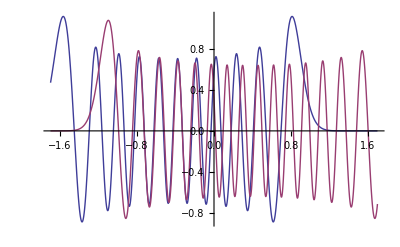

```mathematica
Plot[{HarmWavefunction[20,f1,x+d/2],HarmWavefunction[30,f1,x-d/2]},{x,-1.7,1.7},PlotRange->All]
```

Overlap integrals:

```mathematica
HarmOverlap[n1_,n2_,f1_,f2_,d_,OptionsPattern[{M->MassH,Acc->100}]]:=Module[{mass,acc,o1,o2,mu,a1,a2,s,A,Prefactor,b1,b2,i,j,Kaux},
acc=OptionValue[Acc];
mass=SetAccuracy[OptionValue[M],acc];
Kaux[i_,j_,a_,b_]:=SetAccuracy[If[OddQ[i+j],0,(i+j-1)!!/(a+b)^((i+j)/2)],acc];
mu=SetAccuracy[mass*Dalton,acc];
o1=SetAccuracy[f1*cm2au,acc];
o2=SetAccuracy[f2*cm2au,acc];
a1=SetAccuracy[(mu*o1),acc];
a2=SetAccuracy[(mu*o2),acc];
s=SetAccuracy[(a1*a2*d^2)/(a1+a2),acc];
A=SetAccuracy[(2*Sqrt[a1*a2])/(a1+a2),acc];
Prefactor=SetAccuracy[Sqrt[(A*Exp[-s])/(2^(n1+n2)*n1!*n2!)],acc];
b1=SetAccuracy[-((d*a2*Sqrt[a1])/(a1+a2)),acc];
b2=SetAccuracy[(d*a1*Sqrt[a2])/(a1+a2),acc];
Prefactor*Sum[Binomial[n1,i]*Binomial[n2,j]*HermiteH[n1-i,b1]*HermiteH[n2-j,b2]*(2*Sqrt[a1])^i*(2*Sqrt[a2])^j*Kaux[i,j,a1,a2],{j,0,n2},{i,0,n1}]];
```

## Harmonic bath quantities

Time τ is in ps, temperature T in K and the dimensionless function is actually 1/(π ℏ)Q(τ):

```mathematica
Clear[QS]
```

```mathematica
QS[τ_,T_,OptionsPattern[{Acc->50}]]:=Module[{acc,t,ωc,Ω,β,Gplus,Gminus,G2},
acc=OptionValue[Acc];
t=SetAccuracy[τ,acc];
ωc=SetAccuracy[wc*cm2au,acc];
β=SetAccuracy[1/(kb*T),acc];
Ω=SetAccuracy[1+1/(hbar*β*ωc),acc];
Gplus=SetAccuracy[Gamma[Ω+ⅈ t/(hbar*β)],acc];
Gminus=SetAccuracy[Gamma[Ω-ⅈ t/(hbar*β)],acc];
G2=SetAccuracy[Gamma[Ω]^2,acc];
SetAccuracy[η/π Log[(G2(1+ⅈ ωc t))/(Gplus*Gminus)],acc]];
```

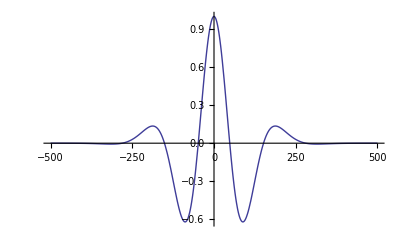

```mathematica
Plot[Re[Exp[-QS[t,300,Acc->20]]],{t,-500,500},PlotRange->All]
```

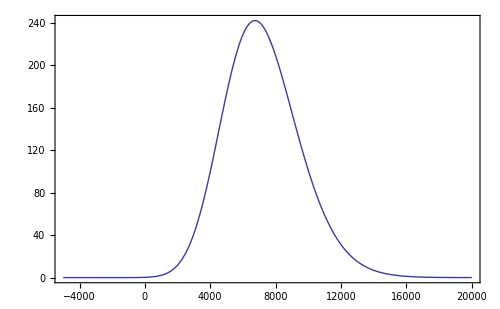
{17.1691,-Graphics-}

```mathematica
ListLinePlot[Table[{x,Re[NIntegrate[SetAccuracy[Exp[ⅈ x cm2au t],30]Exp[-QS[t,300,Acc->30]],{t,-∞,∞},WorkingPrecision->20,MinRecursion->4,MaxRecursion->12,Method->{"DoubleExponential","SymbolicProcessing"->0}]]},{x,-5000,20000,1000}],Axes->False,Frame->True,InterpolationOrder->3]
```

```mathematica
λ kcal2au au2cm
```

7200.

Fourier transform of the e^-QS function:

```mathematica
FQS[ω_,T_,OptionsPattern[{Acc->50}]]:=Module[{acc,fun,omega},
acc=OptionValue[Acc];
omega=SetAccuracy[ω*cm2au,acc];
fun[t_]:=Re[SetAccuracy[Exp[ⅈ omega t],acc]*Exp[-QS[t,T,Acc->acc]]];
2*NIntegrate[fun[t],{t,0,∞},WorkingPrecision->20,MinRecursion->4,MaxRecursion->12,Method->{"DoubleExponential","SymbolicProcessing"->0}]];
```

## Nonadiabatic transition probabilities

Transition probability from |rμ> to |kν> (forward):

```mathematica
Clear[Wforward,Wbackward]
```

```mathematica
Wforward[nu_,mu_,T_,OptionsPattern[{M->MassH,Acc->50}]]:=Module[{emu,enu,acc,Mass,o1,o2,s,s2,prefactor,de,integral},
acc=OptionValue[Acc];
Mass=OptionValue[M];
o1=f1*Sqrt[MassH/Mass];
o2=f2*Sqrt[MassH/Mass];
s=HarmOverlap[mu,nu,o1,o2,d,M->Mass];
s2=s^2;
prefactor=(V*kcal2au)^2*s2;
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
de=-(enu-emu)*kcal2au*au2cm;
integral=If[Abs[de-(η*wc)/π]<10000.0,FQS[de,T,Acc->acc],0];
prefactor*Re[integral]];
```

Transition probability from |kν> to |rμ> (backward):

```mathematica
Wbackward[mu_,nu_,T_,OptionsPattern[{M->MassH,Acc->50}]]:=Module[{acc,Mass,o1,o2,s,s2,prefactor,emu,enu,de,integral},
acc=OptionValue[Acc];
Mass=OptionValue[M];
o1=f1*Sqrt[MassH/Mass];
o2=f2*Sqrt[MassH/Mass];
s=HarmOverlap[mu,nu,o1,o2,d,M->Mass];
s2=s^2;
prefactor=(V*kcal2au)^2*s2;
enu=DG+HarmEnergy[nu,o2];
emu=HarmEnergy[mu,o1];
de=(enu-emu)*kcal2au*au2cm;
integral=If[Abs[de-(η*wc)/π]<10000.0,FQS[de,T,Acc->acc],0];
prefactor*Re[integral]];
```

## Redfield equations and their solution

Number of reactant and product vibronic states:

```mathematica
Nr=35;
Nk=35;
Ntot=Nr+Nk;
```

### Evolution of populations: direct diagonalization of the Redfield matrix

```mathematica
Clear[Rmatrix]
```

```mathematica
Rmatrix[T_,OptionsPattern[{M->MassH,Acc->50}]]:=Module[{mass,acc},
mass=OptionValue[M];
acc=OptionValue[Acc];
Table[
If[i≤Nr,
If[j≤Nr,If[j≠i,0,-Sum[Wforward[k,i-1,T,M->mass,Acc->acc],{k,0,Nk-1}]],Wbackward[i-1,j-Nr-1,T,M->mass,Acc->acc]],
If[j≤Nr,Wforward[i-Nr-1,j-1,T,M->mass,Acc->acc],If[j≠i,0,-Sum[Wbackward[m,i-Nr-1,T,M->mass,Acc->acc],{m,0,Nr-1}]]]]
,{i,1,Ntot},{j,1,Ntot}]];
```

### Redfield matrices

```mathematica
RRH=Rmatrix[300,M->MassH,Acc->50];
```

```mathematica
RRD=Rmatrix[300,M->MassD,Acc->50];
```

```mathematica
diagH=Eigensystem[RRH];
evaluesH=diagH[[1]];
MH=Transpose[diagH[[2]]];
MHr=Inverse[MH];
ΛH=DiagonalMatrix[evaluesH];
```

```mathematica
diagD=Eigensystem[RRD];
evaluesD=diagD[[1]];
MD=Transpose[diagD[[2]]];
MDr=Inverse[MD];
ΛD=DiagonalMatrix[evaluesD];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

```mathematica
Clear[σH,σD]
```

```mathematica
σH[σ0_,t_]:=Module[{Λt,Prop},
Λt=MatrixExp[ΛH t];
Prop=MH . Λt . MHr;
Prop . σ0];
```

```mathematica
σD[σ0_,t_]:=Module[{Λt,Prop},
Λt=MatrixExp[ΛD t];
Prop=MD . Λt . MDr;
Prop . σ0];
```

### Evolution of coherences

```mathematica
σc[i_,j_,σcij0_,T_,t_,OptionsPattern[{M->MassH}]]:=Module[{mass,o1,δω,γ},
mass=OptionValue[M];
o1=f1*Sqrt[MassH/mass]*cm2au;
δω=o1*(i-j);
γ=Sum[Wforward[nu-1,i-1,T,M->mass]+Wbackward[j-1,nu-1,T,M->mass],{nu,1,Nk}];
σcij0*Exp[-ⅈ*δω*t-γ t]
];
```

### Initial reduced density matrix

```mathematica
σ0=Table[0,{i,1,Ntot}];
σ0[[1]]=1;
```

```mathematica
σvH=Table[
If[i≤Nr&&j≤Nr,HarmOverlap[0,i-1,f1,f2,d,M->MassH]*HarmOverlap[0,j-1,f1,f2,d,M->MassH],0],{i,1,Ntot},{j,1,Ntot}
];
```

```mathematica
σvD=Table[
If[i≤Nr&&j≤Nr,HarmOverlap[0,i-1,f1*Sqrt[MassH/MassD],f2*Sqrt[MassH/MassD],d,M->MassD]*HarmOverlap[0,j-1,f1*Sqrt[MassH/MassD],f2*Sqrt[MassH/MassD],d,M->MassD],0],{i,1,Ntot},{j,1,Ntot}
];
```

```mathematica
σvdiagH=Table[σvH[[i,i]],{i,1,Ntot}];
```

```mathematica
σvdiagD=Table[σvD[[i,i]],{i,1,Ntot}];
```

```mathematica
Total[σvdiagH]
```

0.999999999825638391235232498737146923201176124324036007477334871349935637360356118746822

```mathematica
Total[σvdiagD]
```

0.9999996682217394389880964380897639744069458787070332820312958647410565172261843268

Initial populations:

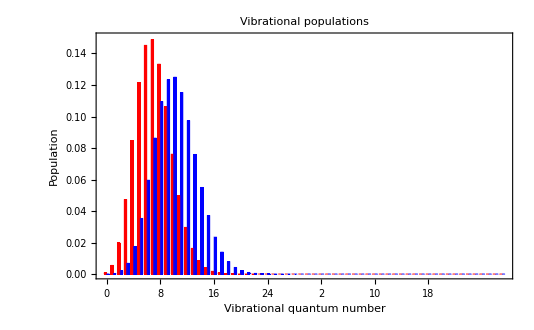

```mathematica
BarChart[{σvdiagH,σvdiagD},BarStyle->{Red,Blue},PlotRange->{0,0.15},FrameLabel->{"Vibrational quantum number","Population"},PlotLabel->"Vibrational populations",Axes->False,Frame->True,BarLabels->Flatten[{Range[0,Nr-1],Range[0,Nk-1]}]]
```

Initial wavepacket (in the reactant electronic state):

```mathematica
Clear[WavevH,WavevD];
```

```mathematica
WavevH[x_]:=Sum[σvH[[i,j]]*HarmWavefunction[i-1,f1,x+d/2,M->MassH]*HarmWavefunction[j-1,f1,x+d/2,M->MassH],{i,1,Nr},{j,1,Nr}];
```

```mathematica
WavevD[x_]:=Sum[σvD[[i,j]]*HarmWavefunction[i-1,f1*Sqrt[MassH/MassD],x+d/2,M->MassD]*HarmWavefunction[j-1,f1*Sqrt[MassH/MassD],x+d/2,M->MassD],{i,1,Nr},{j,1,Nr}];
```

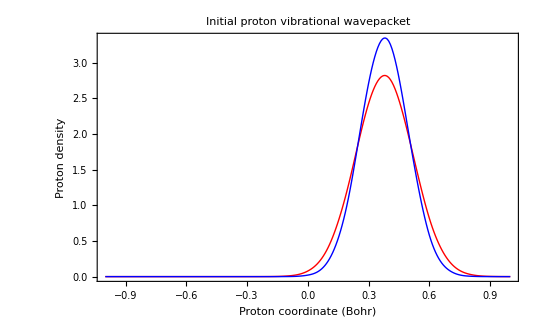

```mathematica
ListLinePlot[{Table[WavevH[x],{x,-1.0,1.0,0.1}],Table[WavevD[x],{x,-1.0,1.0,0.1}]},PlotRange->All,Axes->{False,True},Frame->True,PlotStyle->{Red,Blue},DataRange->{-1.0,1.0},InterpolationOrder->3,FrameLabel->{"Proton coordinate (Bohr)","Proton density"},PlotLabel->"Initial proton vibrational wavepacket"]
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

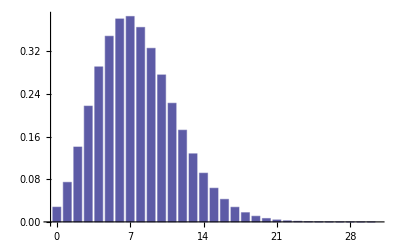

```mathematica
BarChart[Table[HarmOverlap[0,i,f1,f2,d,Acc->100],{i,0,30}],BarLabels->Range[0,30]]
```

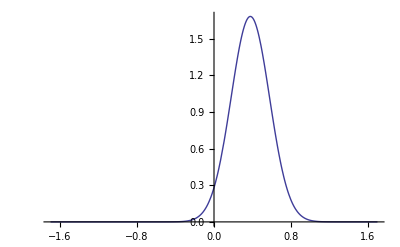

```mathematica
Plot[Sum[HarmOverlap[0,mu,f1,f2,d,Acc->150]*HarmWavefunction[mu,f1,x+d/2],{mu,0,30}],{x,-1.7,1.7}]
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

Distribution of transition probabilities:

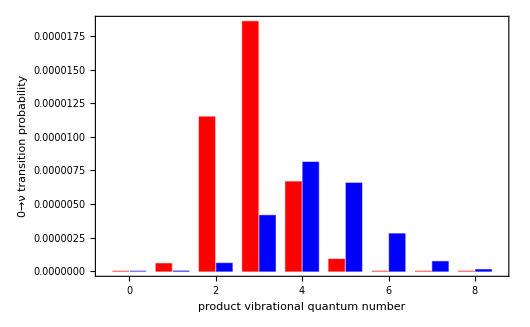

```mathematica
BarChart[{Table[Wforward[0,i,300,M->MassH,Acc->25],{i,0,10}],Table[Wforward[0,i,300,M->MassD,Acc->25],{i,0,10}]},Axes->False,Frame->True,FrameLabel->{"Product vibrational quantum number (ν)","0→ν transition probability"},BarStyle->{Red,Blue},BarOrientation->Vertical,BarLabels->Range[0,10]]
```

### Dynamics of vibrational states populations

```mathematica
Manipulate[BarChart[{σH[σvdiagH,t*ps2au],σD[σvdiagD,t*ps2au]},BarStyle->{Red,Blue},PlotRange->{0,0.15},FrameLabel->{"Vibrational quantum number","Population"},PlotLabel->"Vibrational populations",Axes->False,Frame->True,BarLabels->Flatten[{Range[0,Nr-1],Range[0,Nk-1]}]],{{t,0,"Time (ps)"},0,10,0.01}]
```

### Dynamics of vibrational coherences

```mathematica
Manipulate[BarChart3D[Table[If[i==j,0,Im[σc[i,j,σvH[[i,j]],300,t*ps2au]]],{i,1,Nr},{j,1,Nr}],BarStyle->{Red},PlotRange->{-0.25,0.25},PlotLabel->"Vibrational coherences",Axes->True],{{t,0,"Time (ps)"},0,10,0.01}]
```

```mathematica
el1dataH=Table[Sum[σH[σvdiagH,t*ps2au][[i]],{i,1,Nr}],{t,0,20,0.1}];
el2dataH=Table[Sum[σH[σvdiagH,t*ps2au][[i]],{i,Nr+1,Ntot}],{t,0,20,0.1}];
```

```mathematica
el1dataD=Table[Sum[σD[σvdiagD,t*ps2au][[i]],{i,1,Nr}],{t,0,20,0.1}];
el2dataD=Table[Sum[σD[σvdiagD,t*ps2au][[i]],{i,Nr+1,Ntot}],{t,0,20,0.1}];
```

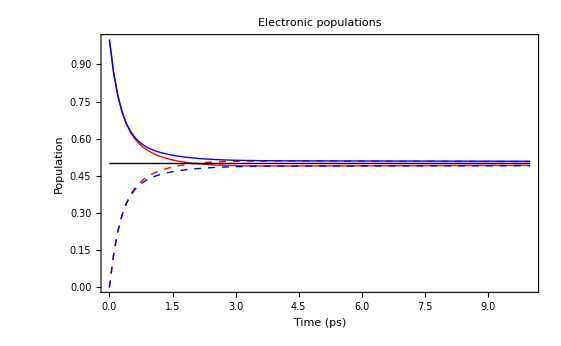

```mathematica
ListLinePlot[{el1dataH,el2dataH,el1dataD,el2dataD,Table[0.5,{t,0,20,0.1}]},PlotRange->{0,1},Axes->False,Frame->True,DataRange->{0,20},PlotStyle->{Red,{Red,Dashed},Blue,{Blue,Dashed},Black},InterpolationOrder->2,PlotMarkers->None,FrameLabel->{"Time (ps)","Population"},PlotLabel->"Electronic populations"]
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",2,"Flute"]]}]
```

### Dynamics of the proton wavepacket

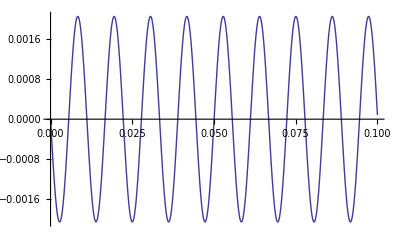

```mathematica
Plot[Im[σc[2,1,σvH[[2,1]],300,t*ps2au]],{t,0,1}]
```

```mathematica
Clear[WavePacket0H,WavePacket0D]
```

```mathematica
WavePacket0H[x_,t_]:=Module[{o1,o2,σvdiag,σdiagt},
o1=f1;
o2=f2;
σdiagt=σH[σ0,t];
{Sum[σdiagt[[i]]*HarmWavefunction[i-1,o1,x+d/2,M->mass]^2,{i,1,Nr}],
Sum[σdiagt[[j]]*HarmWavefunction[j-Nr-1,o2,x-d/2,M->mass]^2,{j,Nr+1,Ntot}]}
];
```

```mathematica
WavePacket0D[x_,t_]:=Module[{o1,o2,σvdiag,σdiagt},
o1=f1 √(MassH/MassD);
o2=f2 √(MassH/MassD);
σdiagt=σD[σ0,t];
{Sum[σdiagt[[i]]*HarmWavefunction[i-1,o1,x+d/2,M->MassD]^2,{i,1,Nr}],
Sum[σdiagt[[j]]*HarmWavefunction[j-Nr-1,o2,x-d/2,M->MassD]^2,{j,Nr+1,Ntot}]}
];
```

```mathematica
σdiagtH=Table[σH[σvdiagH,t*ps2au],{t,0,50,0.2}];
```

```mathematica
σdiagtD=Table[σD[σvdiagD,t*ps2au],{t,0,50,0.2}];
```

```mathematica
Clear[WavePacketv1H,WavePacketv2H,WavePacketv1D,WavePacketv2D]
```

```mathematica
WavePacketv1H=Table[
Sum[If[i==j,σdiagtH[[t,i]]*HarmWavefunction[i-1,f1,x+d/2,M->MassH]^2,σc[i,j,σvH[[i,j]],300,(t-1)*0.1*ps2au]*HarmWavefunction[i-1,f1,x+d/2,M->MassH]*HarmWavefunction[j-1,f1,x+d/2,M->MassH]],{i,1,Nr},{j,1,Nr}],{t,1,251,1},{x,-1.5,1.5,0.1}];
```

```mathematica
WavePacketv2H=Table[
Sum[σdiagtH[[t,i]]*HarmWavefunction[i-1,f2,x-d/2,M->MassH]^2,{i,Nr+1,Ntot}],{t,1,251,1},{x,-1.5,1.5,0.1}];
```

```mathematica
WavePacketv1D=Table[
Sum[If[i==j,σdiagtD[[t,i]]*HarmWavefunction[i-1,f1 √(MassH/MassD),x+d/2,M->MassD]^2,σc[i,j,σvD[[i,j]],300,(t-1)*0.1*ps2au]*HarmWavefunction[i-1,f1 √(MassH/MassD),x+d/2,M->MassD]*HarmWavefunction[j-1,f1 √(MassH/MassD),x+d/2,M->MassD]],{i,1,Nr},{j,1,Nr}],{t,1,251,1},{x,-1.5,1.5,0.1}];
```

```mathematica
WavePacketv2D=Table[
Sum[σdiagtD[[t,i]]*HarmWavefunction[i-1,f2 √(MassH/MassD),x-d/2,M->MassD]^2,{i,Nr+1,Ntot}],{t,1,251,1},{x,-1.5,1.5,0.1}];
```

```mathematica
EmitSound[{Sound[SoundNote["C",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["G",1,"Flute"]],Sound[SoundNote["E",1,"Flute"]],Sound[SoundNote["C",2,"Flute"]],Sound[SoundNote["B",0.5,"Flute"]],Sound[SoundNote["C",2,"Flute"]]}]
```

```mathematica
ListPlot3D[{Re[WavePacketv1H],Re[WavePacketv2H]},PlotRange->All,InterpolationOrder->3,DataRange->{{-1.5,1.5},{0,50}},AxesLabel->{"Proton coordinate (Bohr)","Time (ps)","Amplitude"},PlotLabel->"Time evolution of the vibrational wavepackets (H)",PlotStyle->{LightRed,LightBlue}]
```

-Graphics3D-

```mathematica
ListPlot3D[{Re[WavePacketv1D],Re[WavePacketv2D]},PlotRange->All,InterpolationOrder->3,DataRange->{{-1.5,1.5},{0,50}},AxesLabel->{"Proton coordinate (Bohr)","Time (ps)","Amplitude"},PlotLabel->"Time evolution of the vibrational wavepackets (D)",PlotStyle->{LightRed,LightBlue}]
```

-Graphics3D-